# Сигнальные созвездия

## PSK

Без шума

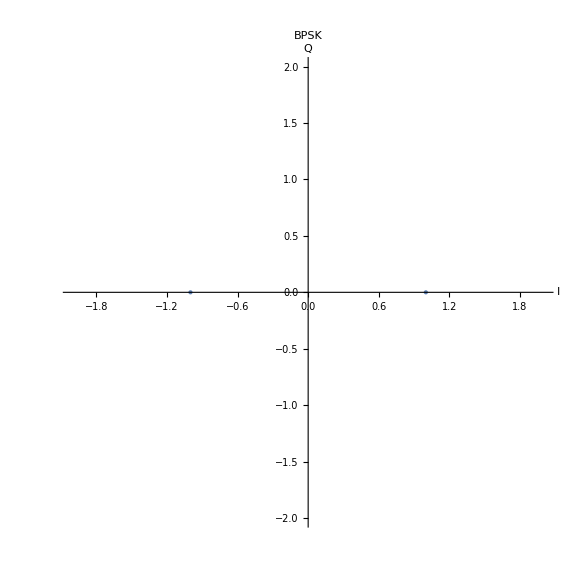

C:\Modulation\Constellation diagram\psk2n0a0.jpg

```mathematica
psk2n0a0=ListPlot[Table[{Cos[i 2π],Sin[i 2π]},{i,0,1-1/2,1/2}],PlotStyle->PointSize[Large],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->Style[Framed["BPSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk2n0a0.jpg",psk2n0a0]
```

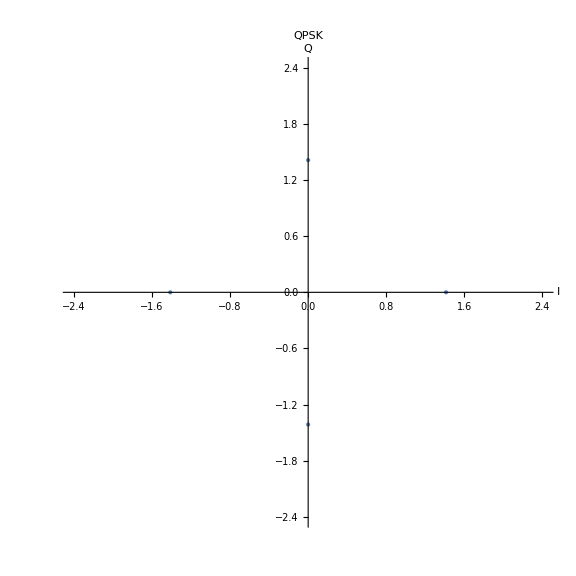

C:\Modulation\Constellation diagram\psk4n0a0.jpg

```mathematica
psk4n0a0=ListPlot[Table[{√2 Cos[i 2π],√2 Sin[i 2π]},{i,0,1-1/4,1/4}],PlotStyle->PointSize[Large],PlotRange->{{-√2-1,√2+1},{-√2-1,√2+1}},AspectRatio->1,PlotLabel->Style[Framed["QPSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk4n0a0.jpg",psk4n0a0]
```

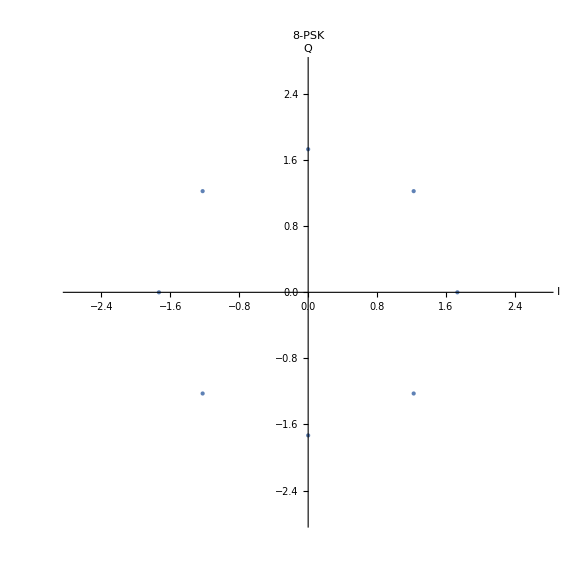

C:\Modulation\Constellation diagram\psk8n0a0.jpg

```mathematica
psk8n0a0=ListPlot[Table[{√3 Cos[i 2π],√3 Sin[i 2π]},{i,0,1-1/8,1/8}],PlotStyle->PointSize[Large],PlotRange->{{-√3-1,√3+1},{-√3-1,√3+1}},AspectRatio->1,PlotLabel->Style[Framed["8-PSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk8n0a0.jpg",psk8n0a0]
```

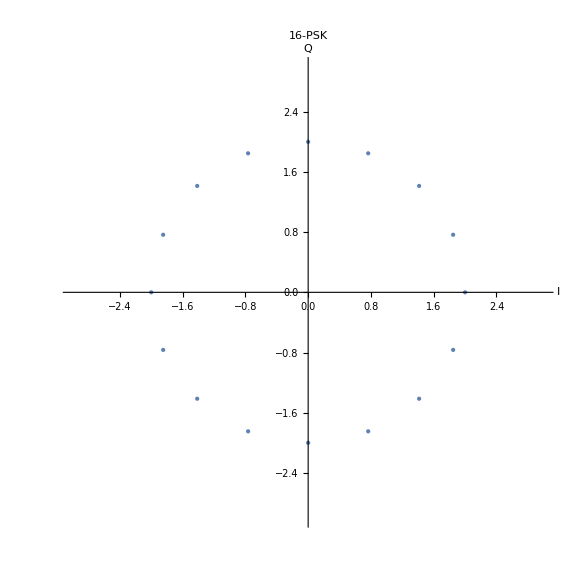

C:\Modulation\Constellation diagram\psk16n0a0.jpg

```mathematica
psk16n0a0=ListPlot[Table[{2Cos[i 2π],2Sin[i 2π]},{i,0,1-1/16,1/16}],PlotStyle->PointSize[Large],PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotLabel->Style[Framed["16-PSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk16n0a0.jpg",psk16n0a0]
```

С шумом Δ∈{-0.1A, 0.1A}

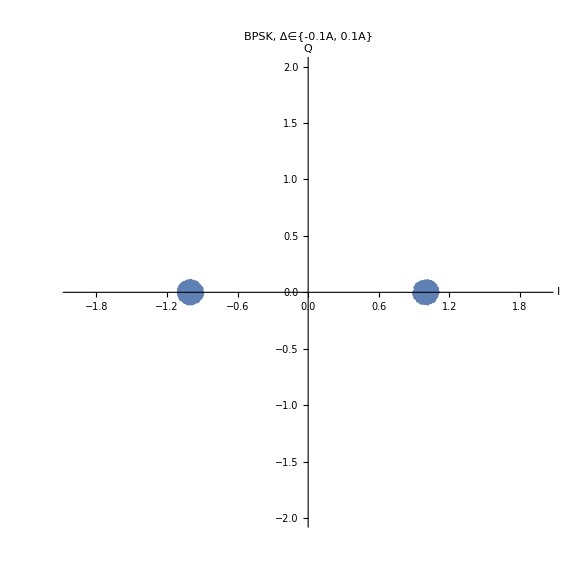

C:\Modulation\Constellation diagram\psk2n1a0.jpg

```mathematica
psk2n1a0=ListPlot[Transpose[Module[{n=2000,m=2,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[Cos[i 2π]],N[Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->Style[Framed["BPSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk2n1a0.jpg",psk2n1a0]
```

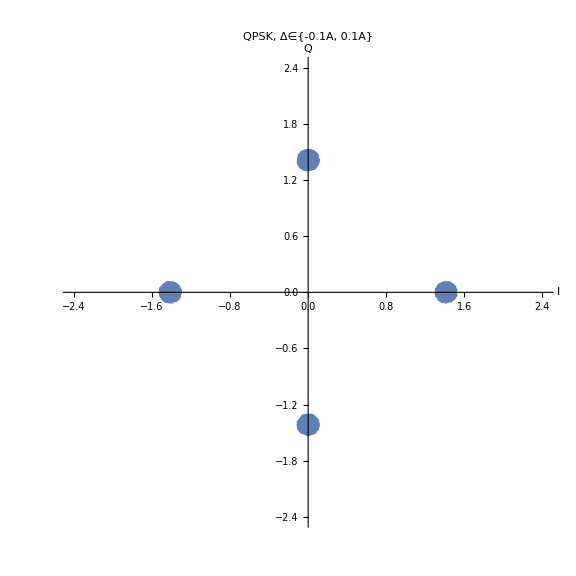

C:\Modulation\Constellation diagram\psk4n1a0.jpg

```mathematica
psk4n1a0=ListPlot[Transpose[Module[{n=4000,m=4,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√2 Cos[i 2π]],N[√2 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√2-1,√2+1},{-√2-1,√2+1}},AspectRatio->1,PlotLabel->Style[Framed["QPSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk4n1a0.jpg",psk4n1a0]
```

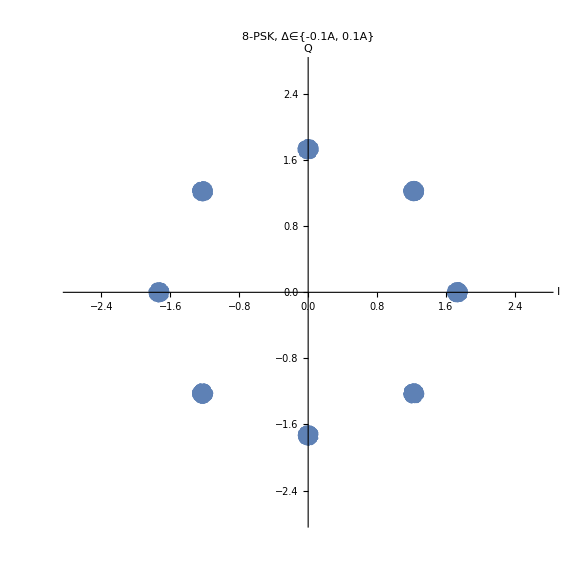

C:\Modulation\Constellation diagram\psk8n1a0.jpg

```mathematica
psk8n1a0=ListPlot[Transpose[Module[{n=8000,m=8,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√3 Cos[i 2π]],N[√3 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√3-1,√3+1},{-√3-1,√3+1}},AspectRatio->1,PlotLabel->Style[Framed["8-PSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk8n1a0.jpg",psk8n1a0]
```

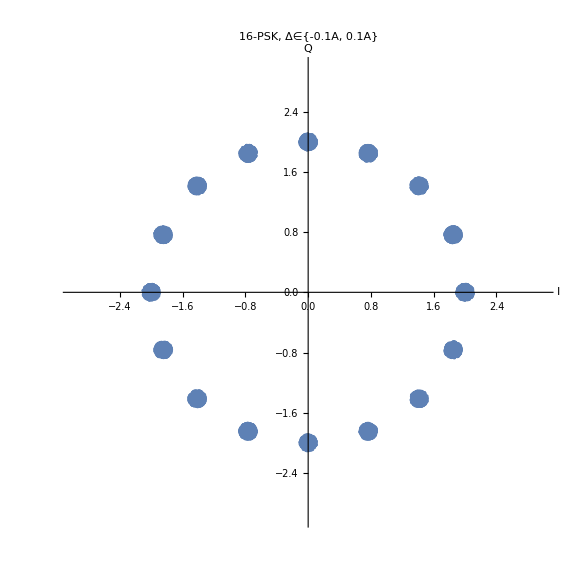

C:\Modulation\Constellation diagram\psk16n1a0.jpg

```mathematica
psk16n1a0=ListPlot[Transpose[Module[{n=16000,m=16,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[2Cos[i 2π]],N[2Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotLabel->Style[Framed["16-PSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk16n1a0.jpg",psk16n1a0]
```

С шумом Δ∈{-0.25A, 0.25A}

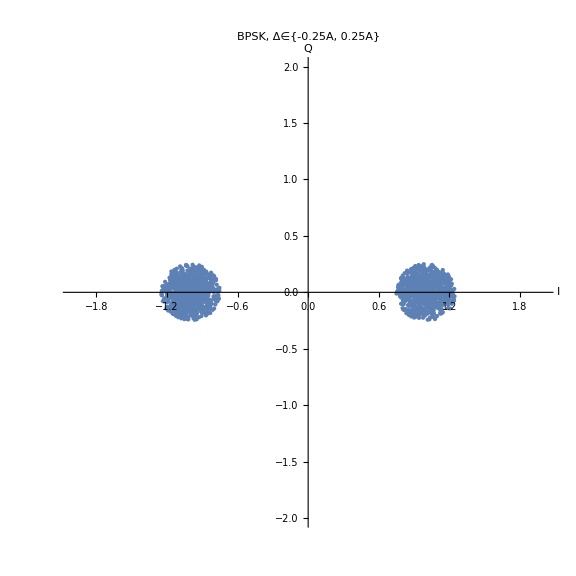

C:\Modulation\Constellation diagram\psk2n2a0.jpg

```mathematica
psk2n2a0=ListPlot[Transpose[Module[{n=2000,m=2,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[Cos[i 2π]],N[Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->Style[Framed["BPSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk2n2a0.jpg",psk2n2a0]
```

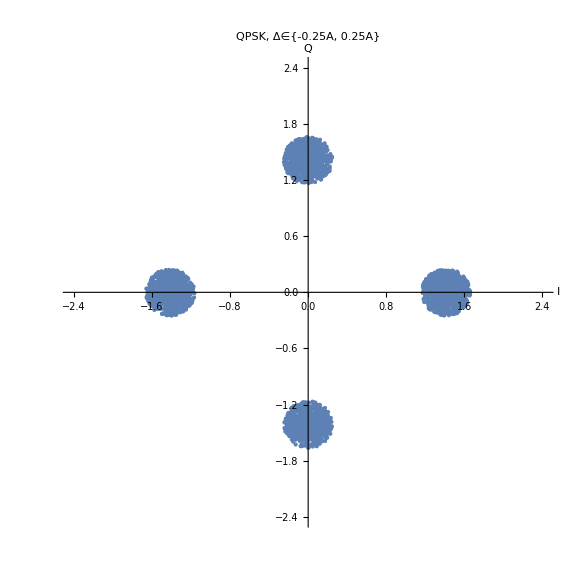

C:\Modulation\Constellation diagram\psk4n2a0.jpg

```mathematica
psk4n2a0=ListPlot[Transpose[Module[{n=4000,m=4,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√2 Cos[i 2π]],N[√2 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√2-1,√2+1},{-√2-1,√2+1}},AspectRatio->1,PlotLabel->Style[Framed["QPSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk4n2a0.jpg",psk4n2a0]
```

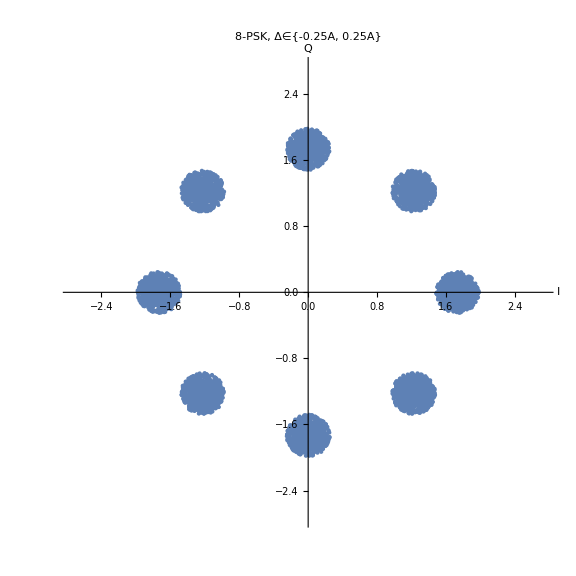

C:\Modulation\Constellation diagram\psk8n2a0.jpg

```mathematica
psk8n2a0=ListPlot[Transpose[Module[{n=8000,m=8,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√3 Cos[i 2π]],N[√3 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√3-1,√3+1},{-√3-1,√3+1}},AspectRatio->1,PlotLabel->Style[Framed["8-PSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk8n2a0.jpg",psk8n2a0]
```

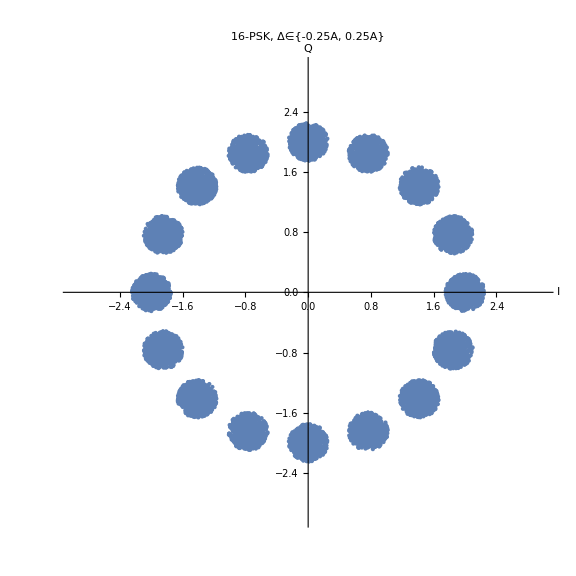

C:\Modulation\Constellation diagram\psk16n2a0.jpg

```mathematica
psk16n2a0=ListPlot[Transpose[Module[{n=16000,m=16,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[2Cos[i 2π]],N[2Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotLabel->Style[Framed["16-PSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk16n2a0.jpg",psk16n2a0]
```

С шумом Δ∈{-0.5A, 0.5A}

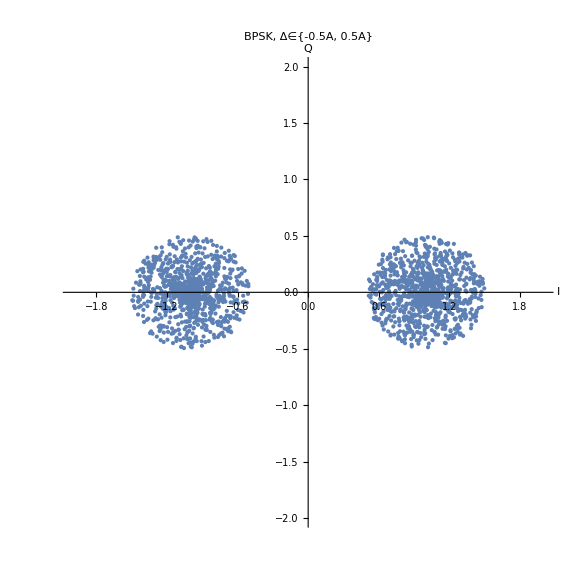

C:\Modulation\Constellation diagram\psk2n3a0.jpg

```mathematica
psk2n3a0=ListPlot[Transpose[Module[{n=2000,m=2,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[Cos[i 2π]],N[Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->Style[Framed["BPSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk2n3a0.jpg",psk2n3a0]
```

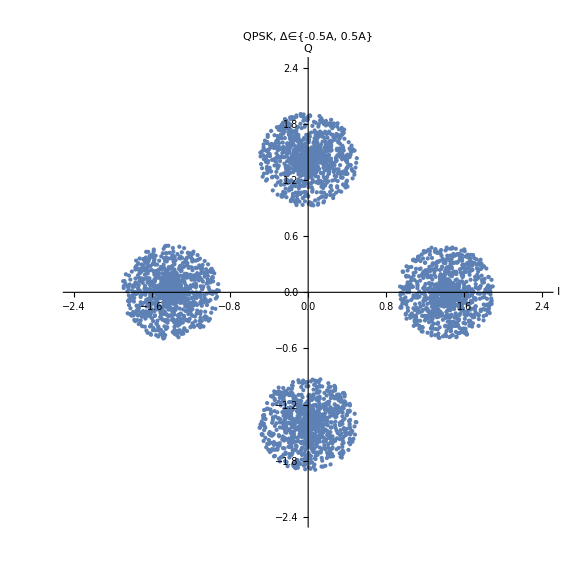

C:\Modulation\Constellation diagram\psk4n3a0.jpg

```mathematica
psk4n3a0=ListPlot[Transpose[Module[{n=4000,m=4,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√2 Cos[i 2π]],N[√2 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√2-1,√2+1},{-√2-1,√2+1}},AspectRatio->1,PlotLabel->Style[Framed["QPSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk4n3a0.jpg",psk4n3a0]
```

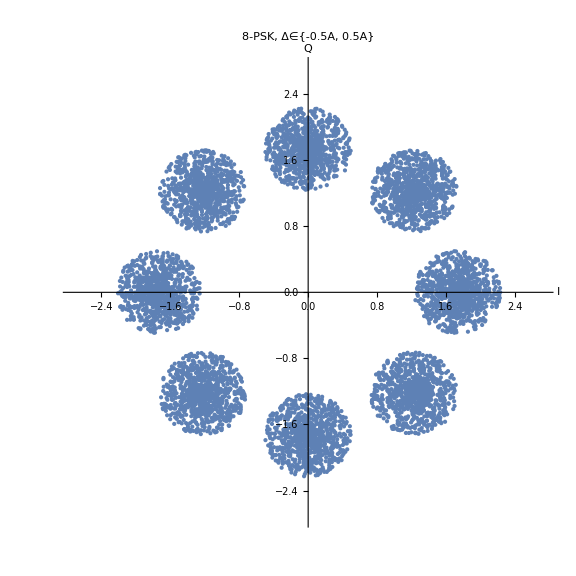

C:\Modulation\Constellation diagram\psk8n3a0.jpg

```mathematica
psk8n3a0=ListPlot[Transpose[Module[{n=8000,m=8,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√3 Cos[i 2π]],N[√3 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√3-1,√3+1},{-√3-1,√3+1}},AspectRatio->1,PlotLabel->Style[Framed["8-PSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk8n3a0.jpg",psk8n3a0]
```

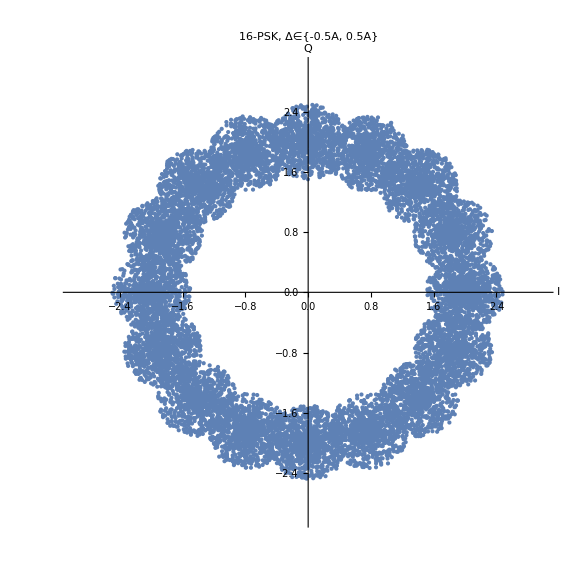

C:\Modulation\Constellation diagram\psk16n3a0.jpg

```mathematica
psk16n3a0=ListPlot[Transpose[Module[{n=16000,m=16,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[2Cos[i 2π]],N[2Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotLabel->Style[Framed["16-PSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk16n3a0.jpg",psk16n3a0]
```

С шумом Δ∈{-1A, 1A}

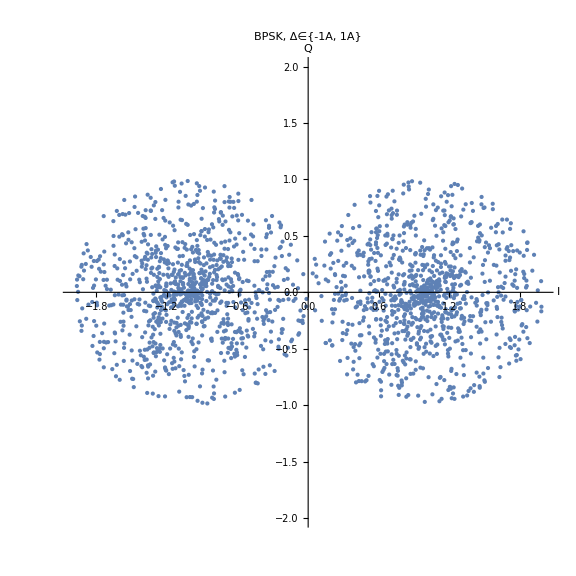

C:\Modulation\Constellation diagram\psk2n4a0.jpg

```mathematica
psk2n4a0=ListPlot[Transpose[Module[{n=2000,m=2,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[Cos[i 2π]],N[Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->Style[Framed["BPSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk2n4a0.jpg",psk2n4a0]
```

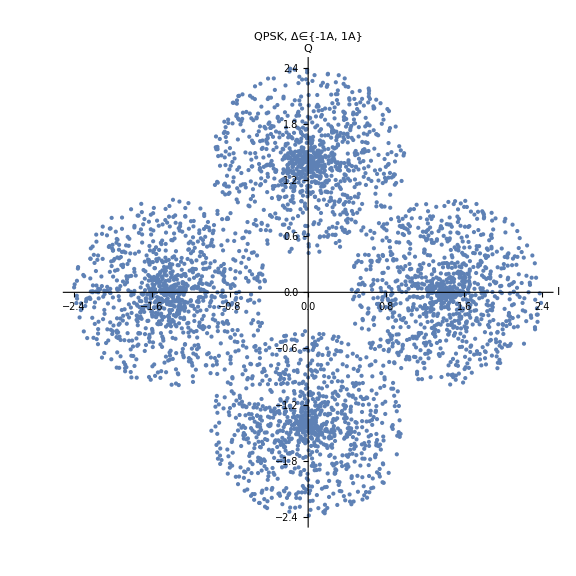

C:\Modulation\Constellation diagram\psk4n4a0.jpg

```mathematica
psk4n4a0=ListPlot[Transpose[Module[{n=4000,m=4,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√2 Cos[i 2π]],N[√2 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√2-1,√2+1},{-√2-1,√2+1}},AspectRatio->1,PlotLabel->Style[Framed["QPSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk4n4a0.jpg",psk4n4a0]
```

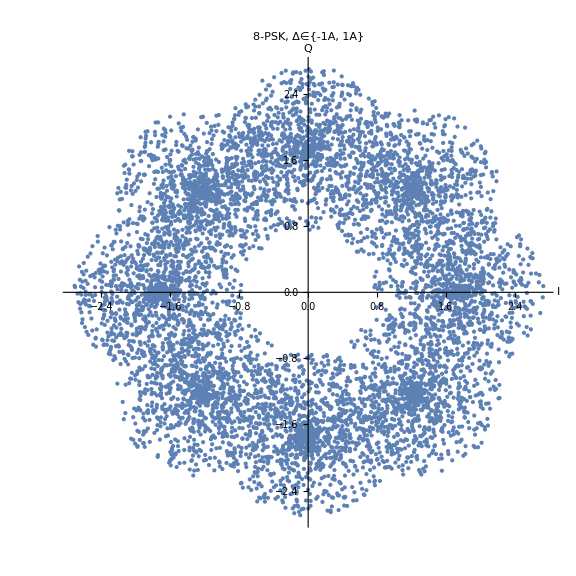

C:\Modulation\Constellation diagram\psk8n4a0.jpg

```mathematica
psk8n4a0=ListPlot[Transpose[Module[{n=8000,m=8,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[√3 Cos[i 2π]],N[√3 Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-√3-1,√3+1},{-√3-1,√3+1}},AspectRatio->1,PlotLabel->Style[Framed["8-PSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk8n4a0.jpg",psk8n4a0]
```

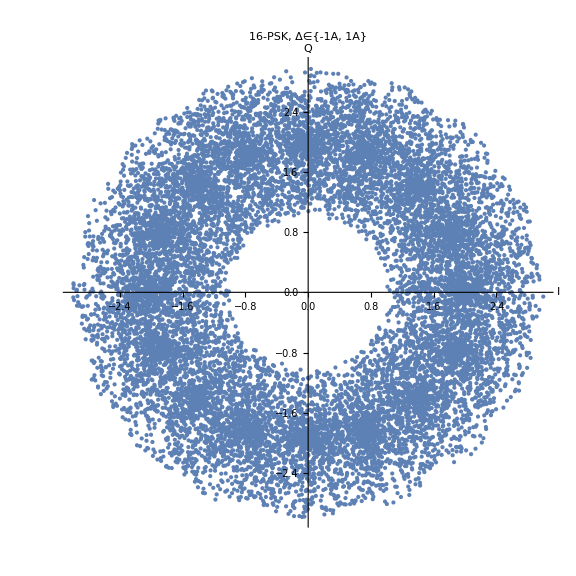

C:\Modulation\Constellation diagram\psk16n4a0.jpg

```mathematica
psk16n4a0=ListPlot[Transpose[Module[{n=16000,m=16,data={},intdata={},andata={}},data=Transpose[RandomChoice[Table[{N[2Cos[i 2π]],N[2Sin[i 2 π]]},{i,0,1-1/m,1/m}],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotLabel->Style[Framed["16-PSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\psk16n4a0.jpg",psk16n4a0]
```